# Linearizing erf approximations to Heaviside functions

We want to use erf based Heaviside approximations.

```mathematica
H[x_, k_] := 0.5 (1 + Erf[k*x])
```

When we do this, what is the linearization of (A0 + A1) H(A0+A1)?

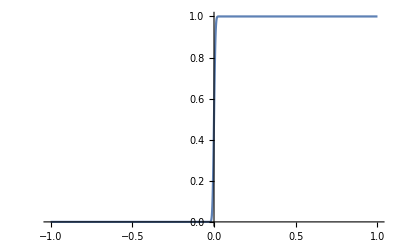

```mathematica
Plot[H[x,10^2], {x,-1,1}]
```

```mathematica
Series[(A0 + A1) H[(A0 + A1), k],{A1,0, 1}]
```

0.5 A0 (1+Erf[A0 k])+0.5 (1+(2 A0 ⅇ^(-A0^2 k^2) k)/(√π)+Erf[A0 k]) A1+O[A1]^2